```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["y_pred.csv","Data"];
b=Import["y_act.csv","Data"];
a=ArrayReshape[a,{20,20,100,4}];
b=ArrayReshape[b,{20,20,100,4}];
Dimensions[a]
```

{20,20,100,4}

1

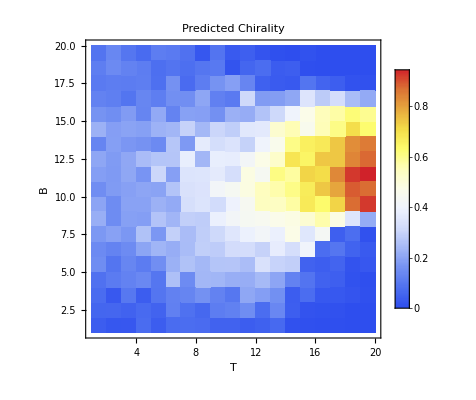

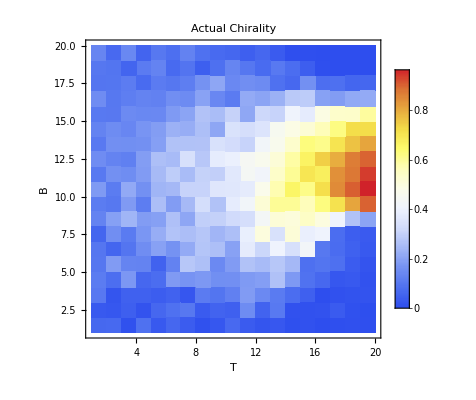

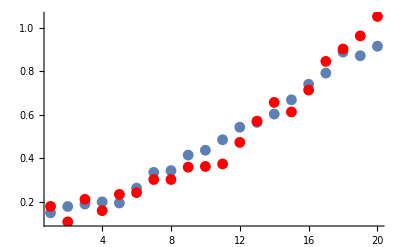

```mathematica
n=1
ListDensityPlot[a[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Predicted Chirality",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
ListDensityPlot[b[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Actual Chirality",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
Show[ListPlot[a[[10,All,95,n]]],ListPlot[b[[10,All,95,n]],PlotStyle->Red],PlotRange->All]
```

2

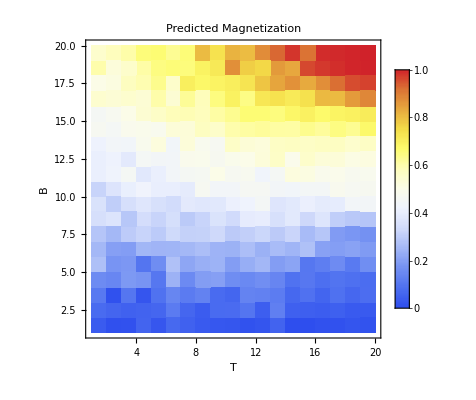

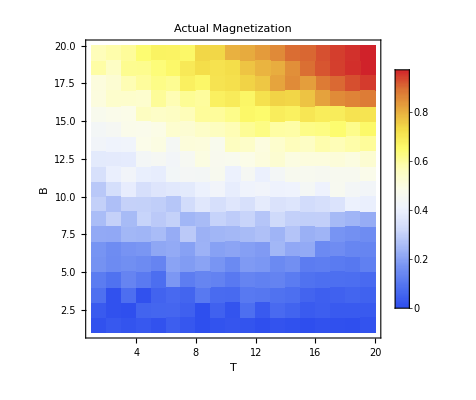

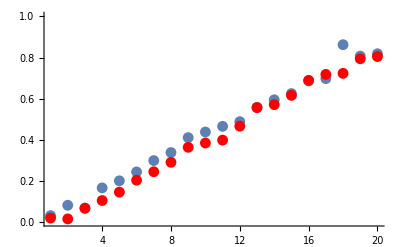

```mathematica
n=2
ListDensityPlot[a[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Predicted Magnetization",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
ListDensityPlot[b[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Actual Magnetization",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
Show[ListPlot[a[[All,10,95,n]]],ListPlot[b[[All,10,95,n]],PlotStyle->Red],PlotRange->{0,1}]
```

3

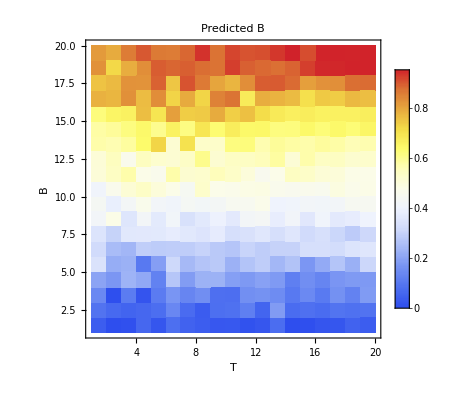

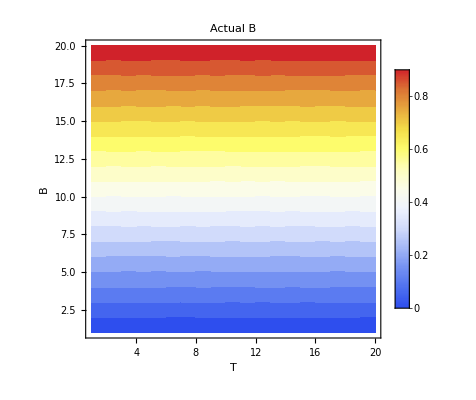

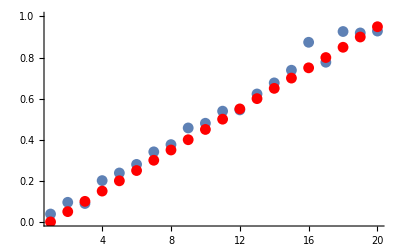

```mathematica
n=3
ListDensityPlot[a[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Predicted B",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
ListDensityPlot[b[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Actual B",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
Show[ListPlot[a[[All,10,95,n]]],ListPlot[b[[All,10,95,n]],PlotStyle->Red],PlotRange->{0,1}]
```

4

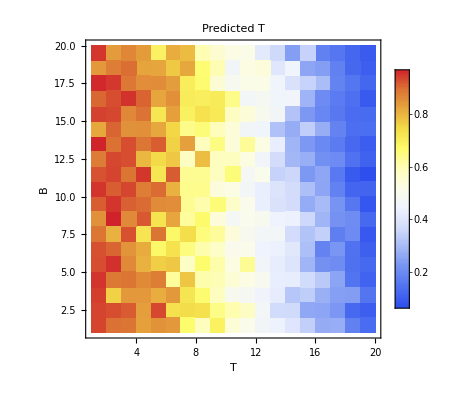

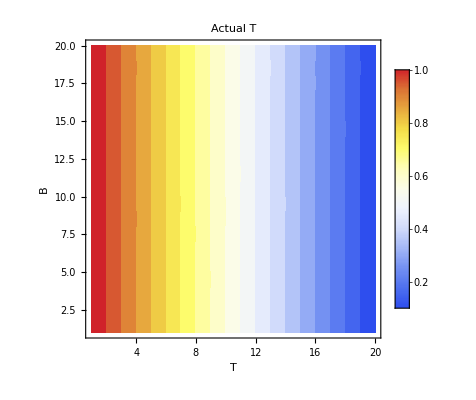

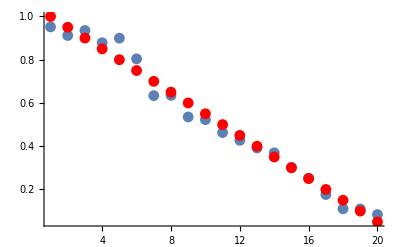

```mathematica
n=4
ListDensityPlot[a[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Predicted T",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
ListDensityPlot[b[[All,All,95,n]],FrameTicks->ftick,ColorFunction->"TemperatureMap",AspectRatio->1,PlotLabel->Style["Actual T",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->0]
Show[ListPlot[a[[10,All,95,n]]],ListPlot[b[[10,All,95,n]],PlotStyle->Red],PlotRange->All]
```